```mathematica
a  =( 1.6*^-19*6.022*^25)/(80*8.8544*^-12);
b = 1.6*^-19/(4.11*^-21);
sol1 = NDSolve[{2 y'[x]+y''[x]x== -a(-ⅇ^(b y[x])+ⅇ^(- b y[x]))x,y[10^-8]== 10^-8,y'[10^-8]== -10},y,{x,10^-10,10^-8}];
```

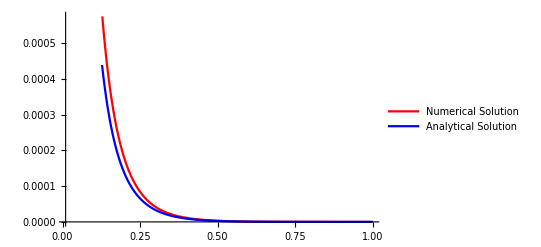

```mathematica
p1 = Plot[y[x]/.sol1,{x,10^-10,10^-8},PlotStyle->Red,PlotLegends->{"Numerical Solution"}];
p2 = Plot[2*^-12 Exp[-10^9*r]/r,{r,10^-10,10^-8},PlotStyle->Blue,PlotLegends->{"Analytical Solution"}];
Show[p1,p2]
```

The numerical solution corresponds well with the linearized theory, as seen in the graph above. 
It does seem reasonable that electrostatic interactions are effectively local, given the very short range over which the potential decays.